### We have a line y_1 = x

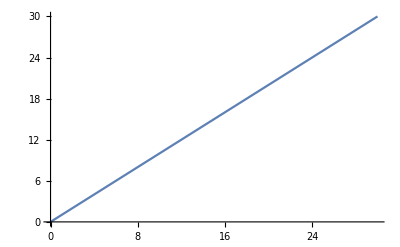

```mathematica
Plot[x,{x,0,30}]
```

### And we have sinusoidal function y_2 = sin(x)

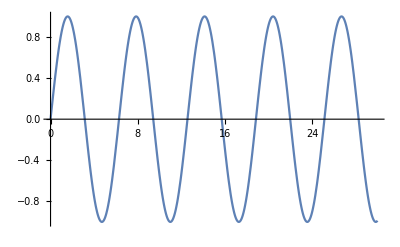

```mathematica
Plot[Sin[x],{x,0,30}]
```

### Then we have product of the two functions y = x sin (x)

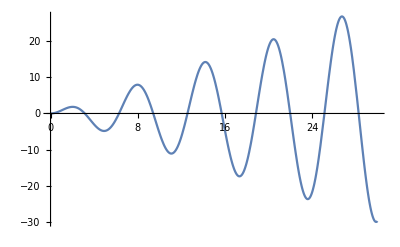

```mathematica
Plot[x Sin[x],{x,0,30}]
```

### And then we have its negative ...

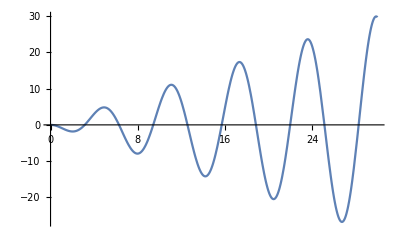

```mathematica
Plot[-x Sin[x],{x,0,30}]
```

### Now lets see them together ...

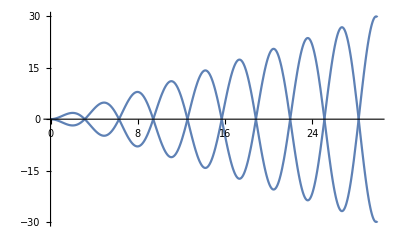

```mathematica
Show[Plot[x Sin[x],{x,0,30}],Plot[-x Sin[x],{x,0,30}],PlotRange->Full]
```

### Its time to get rid of the axes now ...

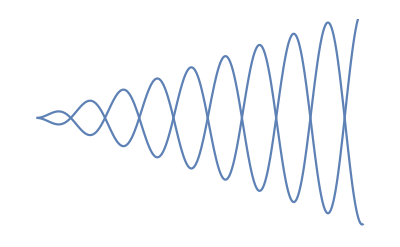

```mathematica
Show[Plot[x Sin[x],{x,0,30}],Plot[-x Sin[x],{x,0,30}],Axes->False]
```

### And rotate the plot by - 90 ° ...

```mathematica
Rotate[Show[Plot[x Sin[x],{x,0,30}],Plot[-x Sin[x],{x,0,30}],Axes->False],-90°]
```

-Graphics-

### Adding a few colors ...

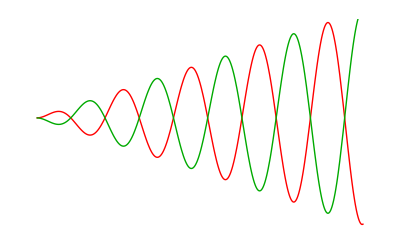

```mathematica
Rotate[Show[Plot[x Sin[x],{x,0,30},PlotStyle->{Red,Thick}],Plot[-x Sin[x],{x,0,30},PlotStyle->{Darker@Green,Thick}],Axes->False],-90°]
```

### And a background ...

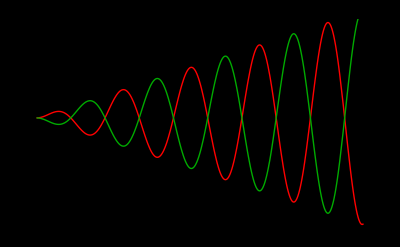

```mathematica
Rotate[Show[Plot[x Sin[x],{x,0,30},PlotStyle->{Red,Thick}],Plot[-x Sin[x],{x,0,30},PlotStyle->{Darker@Green,Thick}],Axes->False,Background->Black],-90°]
```

### A bit of styling ...

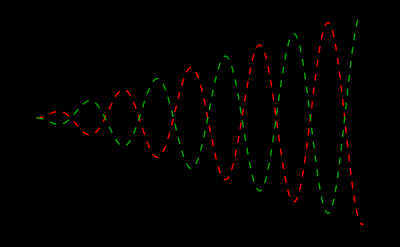

```mathematica
Rotate[Show[Plot[x Sin[x],{x,0,30},PlotStyle->{Red,Thick,Dashed}],Plot[-x Sin[x],{x,0,30},PlotStyle->{Darker@Green,Thick,Dashed}],Axes->False,Background->Black],-90°]
```

### And some snow flakes ...

```mathematica
Overlay[{Rotate[Dynamic[ListPlot[Table[{RandomReal[]*10,RandomReal[]*10},{i,1,20}],PlotMarkers->Style["*",18],Background->Black,Axes->False,PlotStyle->White]],-90°],Rotate[Show[Plot[x Sin[x],{x,0,30},PlotStyle->{Red,Thick,Dashed}],Plot[-x Sin[x],{x,0,30},PlotStyle->{Darker@Green,Thick,Dashed}],Axes->False,Background->Transparent],-90°]}]
```

-Graphics-

### And finally, the animation :)

```mathematica
Animate[Overlay[{Rotate[Dynamic[ListPlot[Table[{RandomReal[]*10,RandomReal[]*10},{i,1,20}],PlotMarkers->Style["*",18],Background->Black,Axes->False,PlotStyle->White,PlotLabel->Style["© Soumya Sambeet Mohapatra",10,Bold,Italic,Darker@White]]],90°],Rotate[Show[Plot[x Sin[x+a],{x,0,30},PlotStyle->{Red,Thick,Dashed}],Plot[-x Sin[x+a],{x,0,30},PlotStyle->{Darker@Green,Thick,Dashed}],Axes->False,Background->Transparent],-90°]}],{a,1,0.01}]
```